```mathematica
On[Assert];
Import[NotebookDirectory[]<>"/DensityMatrixTools.wl"]
```

### Tests

#### Initialize a single q-bit density matrix

```mathematica
ThermalQBit[a,Q1]
```

DM[<|data→SparseArray[…],qbitIDs→<|Q1→1|>,nqbit→1|>]

#### Initialize a 3 q-bit density matrix

```mathematica
ρ1= NThermalQBit[{a1,a2,a3}]
```

DM[<|data→SparseArray[…],qbitIDs→<|𝒬_1→1,𝒬_2→2,𝒬_3→3|>,nqbit→3|>]

#### Inspect a 2 q-bit density matrix

```mathematica
ρ1= NThermalQBit[{a1,a2}];
```

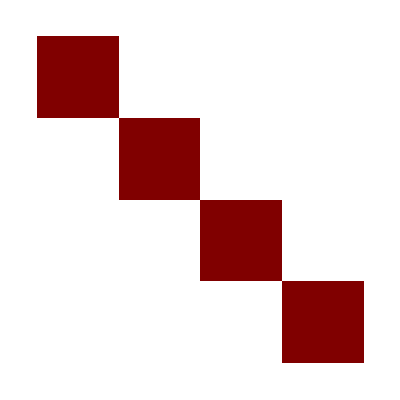

```mathematica
ρ1//Show
```

```mathematica
ρ1//Inspect
```

| 00 | 01 | 10 | 11
00 | (-1+a1) (-1+a2) | 0 | 0 | 0
01 | 0 | a2-a1 a2 | 0 | 0
10 | 0 | 0 | a1-a1 a2 | 0
11 | 0 | 0 | 0 | a1 a2

#### Inspect a 2 q-bit density matrix

```mathematica
ρ1= NThermalQBit[{a1,a2}];
```

```mathematica
ρ1[[2,2]]
```

(1-a1) a2

#### Test Multiplication

Tensor product of two objects in completely distinct Hilbert spaces works. and gives distinct results based on order.

```mathematica
ρ1⊗NThermalQBit[{a2,a3,a4},{Subscript[𝒬, 3],Subscript[𝒬, 4],Subscript[𝒬, 5]}]
```

DM[<|data→SparseArray[…],qbitIDs→<|𝒬_1→1,𝒬_2→2,𝒬_3→3,𝒬_4→4,𝒬_5→5|>,nqbit→5|>]

```mathematica
NThermalQBit[{a2,a3,a4},{Subscript[𝒬, 3],Subscript[𝒬, 4],Subscript[𝒬, 5]}]⊗ρ1
```

DM[<|data→SparseArray[…],qbitIDs→<|𝒬_3→1,𝒬_4→2,𝒬_5→3,𝒬_1→4,𝒬_2→5|>,nqbit→5|>]

Matrix product of two objects in the same Hilbert space works.

```mathematica
ρ1.ρ1
```

DM[<|data→SparseArray[…],qbitIDs→<|𝒬_1→1,𝒬_2→2|>,nqbit→2|>]

These below SHOULD fail, they are invalid operations. 
Matrix product of two objects in different Hilbert spaces is not well defined.
Tensor product of two objects with overlapping Hilbert spaces is not well defined.

```mathematica
ρ1.NThermalQBit[{a2,a3,a4},{Subscript[𝒬, 3],Subscript[𝒬, 4],Subscript[𝒬, 5]}]
```

qBitMissmatch::oob: <|𝒬_1→1,𝒬_2→2|> and <|𝒬_3→1,𝒬_4→2,𝒬_5→3|> must be the same.

```mathematica
ρ1⊗NThermalQBit[{a2,a3,a4},{Subscript[𝒬, 1],Subscript[𝒬, 4],Subscript[𝒬, 5]}]
```

qBitvalue::mismatch: <|𝒬_1→1,𝒬_2→2,𝒬_4→4,𝒬_5→5|> must refrence values in 1...n exactly once each.

#### Test ReOrder

ReOrdering to the same order shouldn’t change a DM.

```mathematica
Assert[ReOrder[ρ1,<| Subscript[𝒬, 1]-> 1,Subscript[𝒬, 2]-> 2|>]==ρ1]
```

ReOrdering to any order and back to the same order should Leave the density matrix unchanged

```mathematica
Assert[ReOrder[ReOrder[ρ1,<| Subscript[𝒬, 1]-> 2,Subscript[𝒬, 2]-> 1|>],<| Subscript[𝒬, 1]-> 1,Subscript[𝒬, 2]-> 2|>]==ρ1]
```

Generating a new density matrix in a different order and reordering should give the same density matrix

```mathematica
Assert[ReOrder[ NThermalQBit[{a2,a1},{Subscript[𝒬, 2],Subscript[𝒬, 1]}],<| Subscript[𝒬, 1]-> 1,Subscript[𝒬, 2]-> 2|>]==ρ1]
```

#### Test Partial Trace

```mathematica
ρ1//Inspect
PTR[ρ1,{Subscript[𝒬, 1]}]//Inspect
PTR[ρ1,{Subscript[𝒬, 2]}]//Inspect
```

| 000 | 001 | 010 | 011 | 100 | 101 | 110 | 111
000 | -((-1+a1) (-1+a2) (-1+a3)) | 0 | 0 | 0 | 0 | 0 | 0 | 0
001 | 0 | (-1+a1) (-1+a2) a3 | 0 | 0 | 0 | 0 | 0 | 0
010 | 0 | 0 | (-1+a1) a2 (-1+a3) | 0 | 0 | 0 | 0 | 0
011 | 0 | 0 | 0 | -((-1+a1) a2 a3) | 0 | 0 | 0 | 0
100 | 0 | 0 | 0 | 0 | a1 (-1+a2) (-1+a3) | 0 | 0 | 0
101 | 0 | 0 | 0 | 0 | 0 | -a1 (-1+a2) a3 | 0 | 0
110 | 0 | 0 | 0 | 0 | 0 | 0 | -a1 a2 (-1+a3) | 0
111 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | a1 a2 a3

| 00 | 01 | 10 | 11
00 | (-1+a2) (-1+a3) | 0 | 0 | 0
01 | 0 | a3-a2 a3 | 0 | 0
10 | 0 | 0 | a2-a2 a3 | 0
11 | 0 | 0 | 0 | a2 a3

| 00 | 01 | 10 | 11
00 | (-1+a1) (-1+a3) | 0 | 0 | 0
01 | 0 | a3-a1 a3 | 0 | 0
10 | 0 | 0 | a1-a1 a3 | 0
11 | 0 | 0 | 0 | a1 a3

The “Complete” trace should give 1.

```mathematica
Assert[(PTR[ρ1,{Subscript[𝒬, 1],Subscript[𝒬, 2]}][data]//Simplify//Normal)=={{1}}]
```

The partial trace should work based on IDs and be independent of supplied order.

```mathematica
Assert[PTR[ NThermalQBit[{a3,a1,a2},{Q3,Q1,Q2}],{Q1,Q2}]===
PTR[ NThermalQBit[{a2,a1,a3},{Q2,Q1,Q3}],{Q1,Q2}]===PTR[ NThermalQBit[{a1,a3,a2},{Q1,Q3,Q2}],{Q1,Q2}]]
```

#### Random Hamiltonians

```mathematica
RandomHamiltonian[1,2]//Inspect
```

| 00 | 01 | 10 | 11
00 | 0 | 0 | 0 | 0
01 | 0 | 0 | ⅈ A[3,2] | 0
10 | 0 | -ⅈ A[3,2] | 0 | 0
11 | 0 | 0 | 0 | 0

```mathematica
RandomHamiltonian[0,3]
RandomHamiltonian[1,3]//Inspect
RandomHamiltonian[2,3]//Inspect
RandomHamiltonian[3,3]
```

0

| 000 | 001 | 010 | 011 | 100 | 101 | 110 | 111
000 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
001 | 0 | 0 | ⅈ A[4,3] | 0 | ⅈ A[4,2] | 0 | 0 | 0
010 | 0 | -ⅈ A[4,3] | 0 | 0 | ⅈ A[3,2] | 0 | 0 | 0
011 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
100 | 0 | -ⅈ A[4,2] | -ⅈ A[3,2] | 0 | 0 | 0 | 0 | 0
101 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
110 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
111 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

| 000 | 001 | 010 | 011 | 100 | 101 | 110 | 111
000 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
001 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
010 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
011 | 0 | 0 | 0 | 0 | 0 | ⅈ A[4,3] | ⅈ A[4,2] | 0
100 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
101 | 0 | 0 | 0 | -ⅈ A[4,3] | 0 | 0 | ⅈ A[3,2] | 0
110 | 0 | 0 | 0 | -ⅈ A[4,2] | 0 | -ⅈ A[3,2] | 0 | 0
111 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

0

### Examples

#### Evolving a 4 q-bit system

```mathematica
ρ = NThermalQBit[{p1,p2,p3,p4}];
Hi = SparseArray[{{13,4}->I,{4,13}-> -I},{16,16}];
Ui =MakeDM[ SparseArray[MatrixExp[I Hi θ]]];
```

```mathematica
Ui.ρ.Transpose[Ui]
```

DM[<|data→SparseArray[…],qbitIDs→<|𝒬_1→1,𝒬_2→2,𝒬_3→3,𝒬_4→4|>,nqbit→4|>]

#### Evolving an 8 q-bit system

Initialize a thermal 8 qbit system.

```mathematica
ρ = NThermalQBit[{p1,p2,p3,p4,p5,p6,p7,p8}];
SubsysInteraction = SparseArray[{{13,4}->I,{4,13}-> -I},{16,16}];
Hi1 = KroneckerProduct[SubsysInteraction,IdentityMatrix[2^4]];
Hi2= KroneckerProduct[IdentityMatrix[2^4],SubsysInteraction];
```

First time step.

```mathematica
Ui =MakeDM[ SparseArray[MatrixExp[I (Hi1+Hi2) θ]]];
ρ = Ui.ρ.Transpose[Ui];
```

Second time step

```mathematica
newOrder =
<|Subscript[𝒬, 1]-> 5,Subscript[𝒬, 2]-> 6,Subscript[𝒬, 3]-> 3,Subscript[𝒬, 4]-> 4,Subscript[𝒬, 5]-> 1,Subscript[𝒬, 6]-> 2,Subscript[𝒬, 7]-> 7,Subscript[𝒬, 8]-> 8|>;
Ui =ReOrder[MakeDM[ SparseArray[MatrixExp[I (Hi1+Hi2) θ]],newOrder],ρ[qbitIDs]];
```

```mathematica
ρ = Ui.ρ.Transpose[Ui];
```

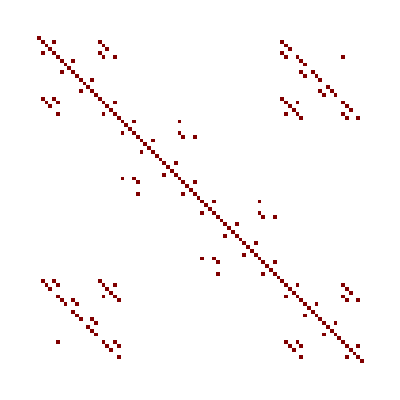

```mathematica
ρ//Show
```